# VYA - Přednášky

## 12. Přednáška

### Interpolace

Věříme hodnotám a hledáme mezi nimi

```mathematica
Quiet[Remove["Global`*"]];
```

{{0.,0.},{0.785398,0.707107},{1.5708,1.},{2.35619,0.707107},{3.14159,1.22465×10^-16},{3.92699,-0.707107},{4.71239,-1.},{5.49779,-0.707107},{6.28319,-2.44929×10^-16}}

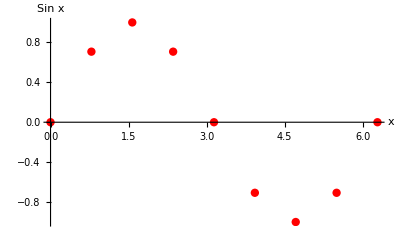

```mathematica
Data = Table[{x, Sin[x]}, {x, 0., 2 Pi, Pi/4}]
PltData = ListPlot[Data, AxesLabel->{"x", "Sin x"}, PlotStyle-> {Red, PointSize[0.015]}, GridLines->Full]
```

```mathematica
?Interpolation
Options[Interpolation]
```

{InterpolationOrder→3,Method→Automatic,PeriodicInterpolation→False}

InterpolatingFunction[…]

{0.,6.28319}

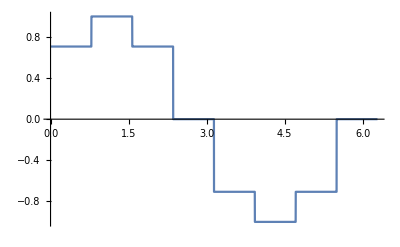

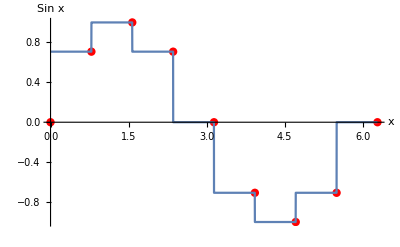

```mathematica
IntSin = Interpolation[Data, InterpolationOrder->0]
{xMin, xMax} = IntSin[[1,1]]
PltInt = Plot[IntSin[x], {x, xMin, xMax}]
Show[PltData, PltInt]
```

```mathematica
?InterpolationOrder
```

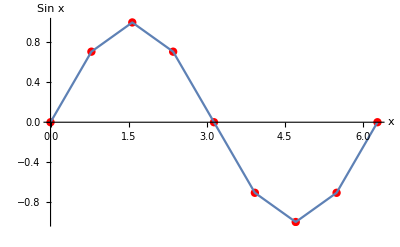

```mathematica
IntSin = Interpolation[Data, InterpolationOrder->1];
PltInt = Plot[IntSin[x], {x, xMin, xMax}];
Show[PltData, PltInt]
```

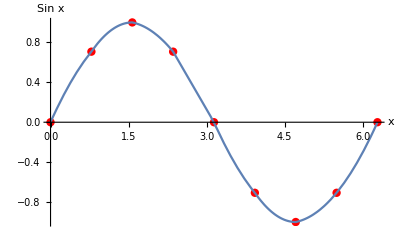

```mathematica
IntSin = Interpolation[Data, InterpolationOrder->2];
PltInt = Plot[IntSin[x], {x, xMin, xMax}];
Show[PltData, PltInt]
```

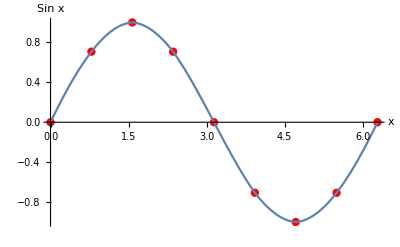

```mathematica
IntSin = Interpolation[Data, InterpolationOrder->3];
PltInt = Plot[IntSin[x], {x, xMin, xMax}];
Show[PltData, PltInt]
```

```mathematica
?InterpolationOrder
```

```mathematica
Quiet[Remove["Global`*"]];
```

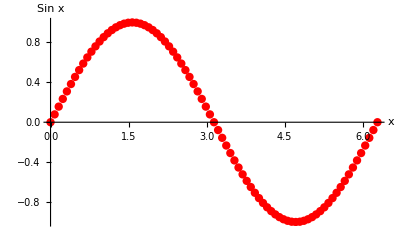

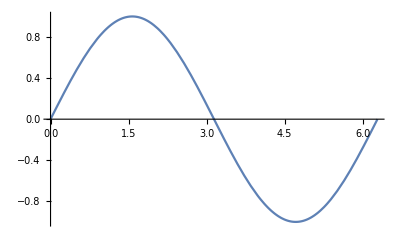

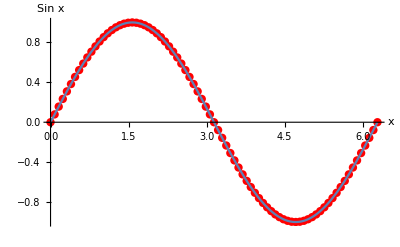

```mathematica
Data = Table[{x, Sin[x]}, {x, 0., 2 Pi, Pi/40}];
PltData = ListPlot[Data, AxesLabel->{"x", "Sin x"}, PlotStyle-> {Red, PointSize[0.015]}, GridLines->Full]
IntSin = Interpolation[Data, InterpolationOrder->3];
{xMin, xMax} = IntSin[[1,1]];
PltInt = Plot[IntSin[x], {x, xMin, xMax}]
Show[PltData, PltInt]
```

```mathematica
Quiet[Remove["Global`*"]];
```

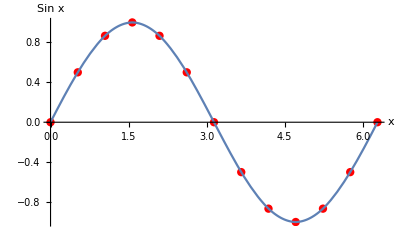

```mathematica
Data = Table[{x, Sin[x]}, {x, 0., 2 Pi, Pi/6}];
PltData = ListPlot[Data, AxesLabel->{"x", "Sin x"}, PlotStyle-> {Red, PointSize[0.015]}, GridLines->Full];
IntSin = Interpolation[Data, InterpolationOrder->3];
{xMin, xMax} = IntSin[[1,1]];
PltInt = Plot[IntSin[x], {x, xMin, xMax}];
Show[PltData, PltInt]
```

InterpolatingFunction::dmval: Input value {-1.5706} lies outside the range of data in the interpolating function. Extrapolation will be used.

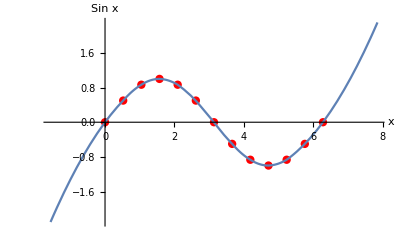

```mathematica
IntSin = Interpolation[Data, InterpolationOrder->2];
PltInt = Plot[IntSin[x], {x, xMin - Pi/2, xMax + Pi/2}];
Show[PltData, PltInt, PlotRange -> All]
```

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
f[y_] := x /. FindRoot[ y == 2x + Sin[x], {x, 0.5y}]
f[5]
```

2.05823

```mathematica
AbsoluteTiming[Table[f[y], {y, 1, 10, 0.001}]][[1]]
```

3.90493

### Put a Get

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\FEL\2. Semestr\Výpočetní Aplikace\Zápisky

```mathematica
Data = Table[{2x - Sin[x], x}, {x, -10, 30, 0.1}];
Funk = Interpolation[Data];
f[y_] := x /. FindRoot[ y == 2x + Sin[x], {x, 0.5y}];
f[5]
```

2.05823

```mathematica
f[5]>> "Funk5"
<< "Funk5"
```

2.05823

```mathematica
?Put
?Get
```

### Table - Matice

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
f[x_, y_] := Sin[x * y + y];
Data3D = Table[{x, y, f[x, y]}, {x, 0, 4, 2}, {y, 0, 3, 1}]
% // MatrixForm
Flatten[Data3D, 1]
Flatten[Data3D]
```

{{{0,0,0},{0,1,Sin[1]},{0,2,Sin[2]},{0,3,Sin[3]}},{{2,0,0},{2,1,Sin[3]},{2,2,Sin[6]},{2,3,Sin[9]}},{{4,0,0},{4,1,Sin[5]},{4,2,Sin[10]},{4,3,Sin[15]}}}

((0
0
0) | (0
1
Sin[1]) | (0
2
Sin[2]) | (0
3
Sin[3])
(2
0
0) | (2
1
Sin[3]) | (2
2
Sin[6]) | (2
3
Sin[9])
(4
0
0) | (4
1
Sin[5]) | (4
2
Sin[10]) | (4
3
Sin[15]))

{{0,0,0},{0,1,Sin[1]},{0,2,Sin[2]},{0,3,Sin[3]},{2,0,0},{2,1,Sin[3]},{2,2,Sin[6]},{2,3,Sin[9]},{4,0,0},{4,1,Sin[5]},{4,2,Sin[10]},{4,3,Sin[15]}}

{0,0,0,0,1,Sin[1],0,2,Sin[2],0,3,Sin[3],2,0,0,2,1,Sin[3],2,2,Sin[6],2,3,Sin[9],4,0,0,4,1,Sin[5],4,2,Sin[10],4,3,Sin[15]}